```mathematica
SetDirectory[NotebookDirectory[]];
```

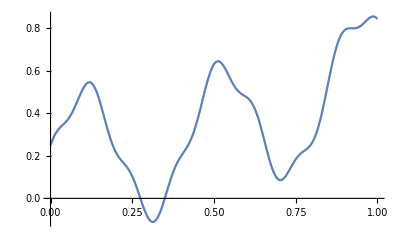

0.25-1.80813 Ramp[-0.98+x]+0.193474 Ramp[-0.96+x]+0.957892 Ramp[-0.94+x]-0.255107 Ramp[-0.92+x]-2.26844 Ramp[-0.9+x]-3.07545 Ramp[-0.88+x]-1.69871 Ramp[-0.86+x]+0.89031 Ramp[-0.84+x]+2.63809 Ramp[-0.82+x]+2.26791 Ramp[-0.8+x]+0.42411 Ramp[-0.78+x]-0.947413 Ramp[-0.76+x]-0.410689 Ramp[-0.74+x]+1.62448 Ramp[-0.72+x]+3.27184 Ramp[-0.7+x]+2.90419 Ramp[-0.68+x]+0.659571 Ramp[-0.66+x]-1.66787 Ramp[-0.64+x]-2.25328 Ramp[-0.62+x]-0.890745 Ramp[-0.6+x]+0.847086 Ramp[-0.58+x]+1.08346 Ramp[-0.56+x]-0.612083 Ramp[-0.54+x]-2.80889 Ramp[-0.52+x]-3.5191 Ramp[-0.5+x]-2.02241 Ramp[-0.48+x]+0.465656 Ramp[-0.46+x]+1.89696 Ramp[-0.44+x]+1.25242 Ramp[-0.42+x]-0.547582 Ramp[-0.4+x]-1.51866 Ramp[-0.38+x]-0.466299 Ramp[-0.36+x]+1.88896 Ramp[-0.34+x]+3.55194 Ramp[-0.32+x]+3.07193 Ramp[-0.3+x]+0.86954 Ramp[-0.28+x]-1.14821 Ramp[-0.26+x]-1.33065 Ramp[-0.24+x]+0.217192 Ramp[-0.22+x]+1.75551 Ramp[-0.2+x]+1.53757 Ramp[-0.18+x]-0.554627 Ramp[-0.16+x]-2.87345 Ramp[-0.14+x]-3.4958 Ramp[-0.12+x]-1.97254 Ramp[-0.1+x]+0.269548 Ramp[-0.08+x]+1.2419 Ramp[-0.06+x]+0.215941 Ramp[-0.04+x]-1.62185 Ramp[-0.02+x]+3.29156 Ramp[0.+x]

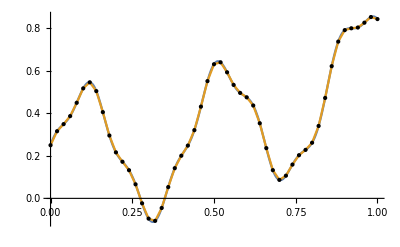

ramp_approx_wl.png

```mathematica
f3[x_] := 0.4*x^2 + 0.3*Sin[15*x] + 0.05*Cos[50*x] + 0.2; 
Plot[f3[x], {x, 0, 1}, AxesOrigin -> {0, 0}, ImageSize -> Full]

step = 0.02; (*discretization step*)
data = ({#1, f3[#1]} & ) /@ Range[0, 1, step]; (*discretized function data*)
h1 = data[[1,2]]; (*first point height*)
inclinations = 1/Apply[Divide, Differences[data], {1}]; 
inclinationChanges = Join[{inclinations[[1]]}, Differences[inclinations]]; 
pa = Transpose[{data[[1 ;; -2,1]], inclinationChanges}]; (*x with inclinaton changes*)
fR[x_] = h1 + Plus @@ (#1[[2]]*Ramp[-#1[[1]] + x] & ) /@ pa
plot = Plot[{f3[x], fR[x]}, {x, 0, 1}, AxesOrigin -> {0, 0}, Epilog -> Point /@ data, ImageSize -> Full]
Export["ramp_approx_wl.png", plot]
```